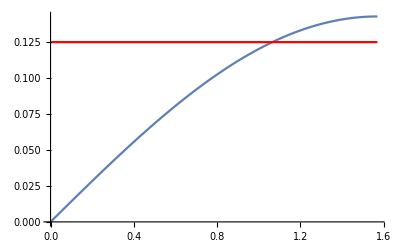

```mathematica
sin[x_, n_, r_] :=  Abs[Sin[ r x]]/(n-r);
f[x_] = sin[x, 8,1];
g[x_,n_] = 1/n;
p1 = Plot[f[x], {x,0,Pi/2},GridLines->{{0,1/8 Pi/2, 1/4 Pi/2, 3/8 Pi/2, 1/2 Pi/2, 5/8 Pi/2, 3/4 Pi/2, 7/8 Pi/2,Pi/2},{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7}}];
p2 = Plot[g[x,8], {x,0,Pi/2}, PlotStyle->Red, GridLines->{{0,1/8 Pi/2, 1/4 Pi/2, 3/8 Pi/2, 1/2 Pi/2, 5/8 Pi/2, 3/4 Pi/2, 7/8 Pi/2},{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7}}];
Show[p1,p2]
```